# SENSORES Y CALIBRACIÓN

ERROR DE GANANCIA, PENDIENTE ≠1 O DE DESPLAZAMIENTO (ORDENADA DIFERENTE A CERO) .

```mathematica
ClearAll["Global'*"]
```

```mathematica
base=ParentDirectory[NotebookDirectory[]]
```

NotebookDirectory::nosv: The notebook 3n3jv_shm is not saved.

ParentDirectory::nums: Argument $Failed should be a positive machine-size integer, a nonempty string, or a File specification.

ParentDirectory[$Failed]

```mathematica
leer[nombre_]:= Rest@Import[FileNameJoin[{base,"datos",nombre},"CSV"]
cal=leer["calibracion_sensor.csv"]
lm=LinearModelFit[cal,u,u]
{a,b}=lm["BestFitParameters"]
lm["ParameterConfidenceIntervals"]
lm["RSquared"]
Sqrt[lm["EstaimatedVariance"]]
Max[Abs[lm["FitResiduals"]]]
corregir[s_]:= (s-a)/b
Corregir[55.5]
enf=lerr["enfriamiento-tanque.csv"];
modelo={Ta+dTExp[-t/tau],{tau,200}};
aj1=NonlinearModelFit[enf,modelo,inicio,t];
aj1["BestFitParameters"]
;
res=aj1["FitResiduals"]
sigR=1.482MedianDeviation[res]
mantener=Flatten@Position[Abs[res-Median[res]],v_/;v≤3 sigR];
quitados = Complement[Range[Length[enf]], mantener]
aj2 = NonlinearModelFit[enf[[mantener]], modelo, inicio, t];
aj2["ParameterTable"]
aj2[300]
tmedio = tau Log[2] /. aj2["BestFitParameters"]
Show[ListPlot[enf, PlotStyle -> Black],
Plot[{aj1[t], aj2[t]}, {t, 0, 600}, PlotStyle -> {Orange, Green}],
AxesLabel -> {"t (s)", "T (C)"}]
```

bestfit parameters : encontar mejor parameter que se ajuste al modelo.
ParameterConfidenceIntervals: son los parametros de pendiente y constante, entre mas cercano entre ellos mejor.

# OPTIMIZACIÓN OPERATIVA

```mathematica
ClearAll["Global'*"]
restr=3*x+2 y≤120 && 2*x+4*y y≤140 && 60*x+40*y≤ 2800 && x≥0 && y≥0
```

3 x+2 y≤120&&2 x+4 y^2≤140&&60 x+40 y≤2800&&x≥0&&y≥0

```mathematica
opt=Maximize[{14000 x +16000,restr},{x,y}]
```

{576000,{x→40,y→0}}

```mathematica
restr && Element[x, Integers] && Element[y, Integers]
```

3 x+2 y≤120&&2 x+4 y^2≤140&&60 x+40 y≤2800&&x≥0&&y≥0&&x∈ℤ&&y∈ℤ

```mathematica
Maximize[{14000 x + 16000 y,
restr && Element[x, Integers] && Element[y, Integers]}, {x, y}]
```

{582000,{x→37,y→4}}

```mathematica
{120 - (3 x + 2 y), 140 - (2 x + 4 y), 2800 - (60 x + 40 y)} /. opt[[2]]
```

{0,60,400}

```mathematica
utilidad[h_] := First@Maximize[{14000 x + 16000 y,
3 x + 2 y <= 120 && 2 x + 4 y <= h && 60 x + 40 y <= 2800 &&
x >= 0 && y >= 0}, {x, y}]
Table[{h, utilidad[h]}, {h, 130, 150, 10}]
```

{{130,685000},{140,710000},{150,735000}}

```mathematica
Maximize[{14000 x + 9000 y, restr}, {x, y}]
```

{560000,{x→40,y→0}}

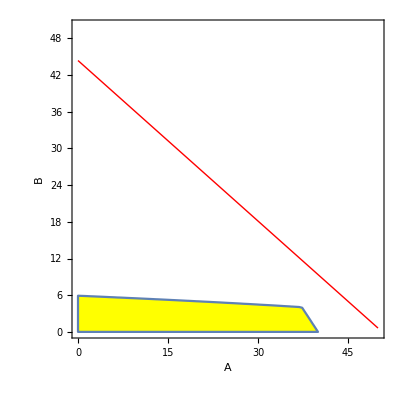

```mathematica
Show[RegionPlot[restr, {x, 0, 50}, {y, 0, 50}, PlotStyle -> Yellow],
ContourPlot[14000 x + 16000 y == 710000, {x, 0, 50}, {y, 0, 50},
ContourStyle -> {Red, Thick}], AxesLabel -> {"A", "B"}]
```

{710000,{x→25,y→45/2}}

{0,0,400}

{704000,{x→24,y→23}}

{{130,685000},{140,710000},{150,735000}}

{560000,{x→40,y→0}}

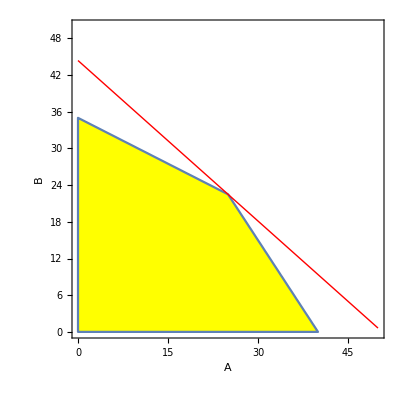

```mathematica
ClearAll["Global`*"];
restr=3 x+2 y≤120&&2 x+4 y≤140&&60 x+40 y≤2800&&x≥0&&y≥0;
opt=Maximize[{14000 x+16000 y,restr},{x,y}]
{120-(3 x+2 y),140-(2 x+4 y),2800-(60 x+40 y)}/.opt[[2]]
Maximize[{14000 x+16000 y,restr&&Element[x,Integers]&&Element[y,Integers]},{x,y}]
utilidad[h_]:=First@Maximize[{14000 x+16000 y,3 x+2 y≤120&&2 x+4 y≤h&&60 x+40 y≤2800&&x≥0&&y≥0},{x,y}]
Table[{h,utilidad[h]},{h,130,150,10}]
Maximize[{14000 x+9000 y,restr},{x,y}]
Show[RegionPlot[restr,{x,0,50},{y,0,50},PlotStyle->Yellow],ContourPlot[14000 x+16000 y==710000,{x,0,50},{y,0,50},ContourStyle->{Red,Thick}],AxesLabel->{"A","B"}]
```